```mathematica
(* Problem 0 Happy Valentune's Day *)
```

```mathematica
ContourPlot3D[(2x^2+y^2+z^2-1)^3-(1/10)x^2z^3-y^2z^3==0,{x,-1.5,1.5},{y,-1.5,1.5},{z,-1.5,1.5}, Mesh->None,ContourStyle->Opacity[0.9,Red]]
```

-Graphics3D-

```mathematica
(* Problem 1 1D *)
```

```mathematica
fSin[t_]:={t,Sin[t^2]}
```

```mathematica
(* Define 30 points on the interval [0, 4P] *)
```

```mathematica
Clear[fx]
```

```mathematica
fx[x_]:=1.0*x
```

```mathematica
P100=Array[fx,100,{0,2Pi}];
```

```mathematica
P100S = Map[fSin,P100];
```

```mathematica
(* Plot *)
```

```mathematica
Points100S = Point[P100S];
```

```mathematica
Lines100S = Line[P100S];
```

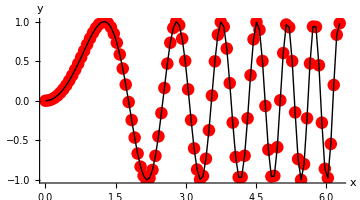

```mathematica
GP100S=Graphics[{{Red,PointSize->0.025,Points100S},Lines100S},Axes->True,ImageSize->Medium]
```

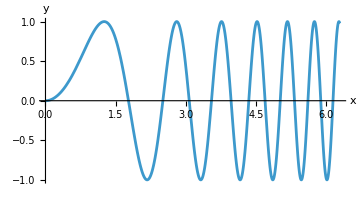

```mathematica
ParametricPlot[fSin[t],{t,0,2Pi},ImageSize->Medium]
```

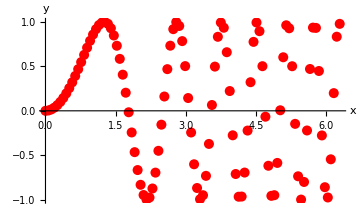

```mathematica
L1 = ListPlot[P100S,ImageSize->Medium,PlotStyle->{Red,PointSize[0.02]}]
```

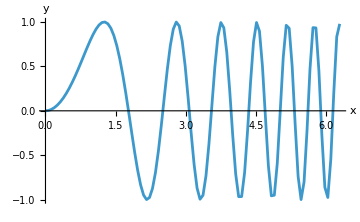

```mathematica
L2=ListPlot[P100S,ImageSize->Medium,Joined->True]
```

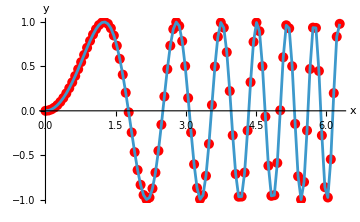

```mathematica
Show[L1,L2]
```

```mathematica
(* Problem 2 *)
```

```mathematica
c = 10
```

10

```mathematica
R = 2
```

2

```mathematica
ft[t_] := t
```

```mathematica
f2[t_] := {R Sin[t]Cos[c*t],R Sin[t]Sin[c*t],R Cos[t]}
```

```mathematica
P100 = Array[ft, 100,{0,2Pi}]
```

{0,(2 π)/99,(4 π)/99,(2 π)/33,(8 π)/99,(10 π)/99,(4 π)/33,(14 π)/99,(16 π)/99,(2 π)/11,(20 π)/99,(2 π)/9,(8 π)/33,(26 π)/99,(28 π)/99,(10 π)/33,(32 π)/99,(34 π)/99,(4 π)/11,(38 π)/99,(40 π)/99,(14 π)/33,(4 π)/9,(46 π)/99,(16 π)/33,(50 π)/99,(52 π)/99,(6 π)/11,(56 π)/99,(58 π)/99,(20 π)/33,(62 π)/99,(64 π)/99,(2 π)/3,(68 π)/99,(70 π)/99,(8 π)/11,(74 π)/99,(76 π)/99,(26 π)/33,(80 π)/99,(82 π)/99,(28 π)/33,(86 π)/99,(8 π)/9,(10 π)/11,(92 π)/99,(94 π)/99,(32 π)/33,(98 π)/99,(100 π)/99,(34 π)/33,(104 π)/99,(106 π)/99,(12 π)/11,(10 π)/9,(112 π)/99,(38 π)/33,(116 π)/99,(118 π)/99,(40 π)/33,(122 π)/99,(124 π)/99,(14 π)/11,(128 π)/99,(130 π)/99,(4 π)/3,(134 π)/99,(136 π)/99,(46 π)/33,(140 π)/99,(142 π)/99,(16 π)/11,(146 π)/99,(148 π)/99,(50 π)/33,(152 π)/99,(14 π)/9,(52 π)/33,(158 π)/99,(160 π)/99,(18 π)/11,(164 π)/99,(166 π)/99,(56 π)/33,(170 π)/99,(172 π)/99,(58 π)/33,(16 π)/9,(178 π)/99,(20 π)/11,(182 π)/99,(184 π)/99,(62 π)/33,(188 π)/99,(190 π)/99,(64 π)/33,(194 π)/99,(196 π)/99,2 π}

```mathematica
P100S = Map[f2,P100];
```

```mathematica
Points100 = Point[P100S];
```

```mathematica
Lines100 = Line[P100S];
```

```mathematica
GP100S2 = Graphics3D[{{Red,PointSize->0.025,Points100},Lines100}, Axes->True, ImageSize->Medium,BoxRatios->1 ]
```

-Graphics3D-

```mathematica
ListPoint100 = ListPointPlot3D[P100S, Axes->True, ImageSize->Medium, PlotStyle->{Purple,PointSize[0.02]},BoxRatios->1 ]
```

-Graphics3D-

```mathematica
ListLine100 = ListLinePlot3D[P100S, Axes->True, ImageSize->Medium, PlotStyle->{Blue,PointSize[0.02]},BoxRatios->{2,2,1} ]
```

-Graphics3D-

```mathematica
Show[{ListPoint100,ListLine100}]
```

-Graphics3D-

```mathematica
(* Self Study, What about if Show[{ListLine100,ListPoint100}] -> the aspect ratio will applied as well haha *)
```

```mathematica
(* ParametricPlot3D and Graphics3D/Point *)
```

```mathematica
Parametric100t = ParametricPlot3D[f2[t],{t,0,2Pi},ImageSize->Medium,PlotRange->{{-2,2},{-2,2},{-2,2}}] (* Smooth กว่า Line มาก *)
```

-Graphics3D-

```mathematica
Point100Red = Graphics3D[{{Red,PointSize->0.02,Points100}}, Axes->True, ImageSize->Medium ]
```

-Graphics3D-

```mathematica
Show[{Parametric100t,Point100Red}]
```

-Graphics3D-

```mathematica
(* 3D Graphs *)
```

```mathematica
R=10
```

10

```mathematica
Sp3[u_]:={Cos[u],Sin[u]+Sqrt[Abs[Cos[u]]],u}
```

```mathematica
ParametricPlot3D[Sp3[t],{t,0,8*Pi},BoxRatios->1]
```

-Graphics3D-

```mathematica
(* List of random colors *)
```

```mathematica
ListColors1 = Table[RandomColor[],{i,5}]
```

{RGBColor[0.6176945941819312, 0.9488116567997564, 0.06628024832758284],RGBColor[0.4500156395190045, 0.6973436682326732, 0.43433932305790535],RGBColor[0.6580925386388303, 0.07174780912768397, 0.5499757080065442],RGBColor[0.19456964515212039, 0.06555631518047522, 0.8748608127961399],RGBColor[0.5931559012860406, 0.07182519317070657, 0.5162660542306854]}

```mathematica
(* Graphic Function *)
```

```mathematica
GCone[Color_]:=ParametricPlot3D[Sp3[t],{t,0,8*Pi},BoxRatios->1,PlotStyle->{Color,Thickness[0.025]}]
```

```mathematica
GListCone1=Table[GCone[ListColors1[[i]]],{i,Length[ListColors1]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
GListCone12=Map[GCone,ListColors1] (* แค่โชว์ว่า Map จะง่ายกว่าไล่ Array ทีละตัว *)
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Problem 4 *)
```

```mathematica
ListThickness = Table[Thickness[0.01+0.005i],{i,5}]
```

{Thickness[0.015],Thickness[0.02],Thickness[0.025],Thickness[0.03],Thickness[0.035]}

```mathematica
Clear[GCone2]
```

```mathematica
GCone2[Color_,Thickness_] :=ParametricPlot3D[Sp3[t],{t,0,8*Pi},BoxRatios->1,PlotStyle->{Color,Thickness}]
```

```mathematica
GListCone2= Table[GCone2[ListColors1[[i]],ListThickness[[i]]],{i,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Problem 5 *)
```

```mathematica
ListType1={0,Dotted,Dashed,DotDashed,0}
```

{0,Dashing[{0,Small}],Dashing[{Small,Small}],Dashing[{0,Small,Small,Small}],0}

```mathematica
GCone3[Color_,Dotted_]:= ParametricPlot3D[Sp3[t],{t,0,8Pi},BoxRatios->1,PlotStyle->{Color,Dotted}]
```

```mathematica
GlistCone3 = Table[GCone3[ListColors1[[i]],ListType1[[i]]],{i,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Problem 6 *)
```

```mathematica
R1=1
```

1

```mathematica
R2=2
```

2

```mathematica
S1=ParametricPlot3D[{R1 Cos[#1]×Sin[#2],R1 Sin[#1]×Sin[#2],R2 Cos[#2]}&[u,v],{u,0,Pi},{v,0,2Pi}]
```

-Graphics3D-

```mathematica
R1=2
```

2

```mathematica
R2=1
```

1

```mathematica
S2=ParametricPlot3D[{R1 Cos[#1]×Sin[#2],R1 Sin[#1]×Sin[#2],R2 Cos[#2]}&[u,v],{u,0,Pi},{v,0,2Pi}] (* เหมือนข้างบน 100% แค่เปลี่ยน R1, R2 *)
```

-Graphics3D-

```mathematica
Show[{S1,S2},PlotRange->2]
```

-Graphics3D-

```mathematica
Sphere1= Graphics3D[{Opacity[0.1],Brown,Sphere[{0,0,0},R1]}]
```

-Graphics3D-

```mathematica
Show[{S1,S2,Sphere1},PlotRange->2]
```

-Graphics3D-

```mathematica
(* Problem 7 *)
```

```mathematica
R = 2
```

2

```mathematica
x[u_,v_]:=(R+v Sin[u/2]) Cos[u];
```

```mathematica
y[u_,v_]:=(R+v Sin[u/2]) Sin[u];
```

```mathematica
z[u_, v_]:=v Cos[u/2]
```

```mathematica
(* Meobius strip for {u, pi/3, 5pi/3} *)
```

```mathematica
m1=ParametricPlot3D[{x[u,v],y[u,v],z[u,v]},{u,Pi/3,5* Pi/3},{v,-1/2,1/2},PlotStyle->{Blue,Opacity[0.3]}]
```

-Graphics3D-

```mathematica
m2 = ParametricPlot3D[{x[u,v], y[u,v],z[u,v]},{u,4Pi/3,8Pi/3},{v,-1/2,1/2},PlotStyle->{Blue, Opacity[0.3]}]
```

-Graphics3D-

```mathematica
Show[{m1,m2},PlotRange->2.5,BoxRatios->1]
```

-Graphics3D-

```mathematica
s1 = SphericalPlot3D[1+R Cos[2t],{t,0,Pi},{u,0,2Pi}]
```

-Graphics3D-

```mathematica
Show[{s1,m1,m2},PlotRange->3]
```

-Graphics3D-

```mathematica
(* Problem 8 *)
```

```mathematica
GS[R_]:=SphericalPlot3D[1+R Cos[2*t], {t,0,Pi},{u,0,2*Pi}]
```

```mathematica
GT5 = Table[SphericalPlot3D[1 +R Cos[2*t],{t,0,Pi},{u,0,2Pi},PlotRange->{{-4,4},{-4,4},{-6,6}}],{R,1,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[GT5,AnimationRunning->False]
```

```mathematica
(* Problem 9 *)
```

```mathematica
M1[Color_] := ParametricPlot3D[{x[u,v],y[u,v],z[u,v]},{u,Pi/3,5*Pi/3},{v,-1/2,1/2},PlotStyle->{Color,Opacity[0.3]}]
```

```mathematica
M2[Color_] := ParametricPlot3D[{x[u,v],y[u,v],z[u,v]},{u,Pi/3,5*Pi/3},{v,-1/2,1/2},PlotStyle->{Color,Opacity[0.3]}] (* Same as above *)
```

```mathematica
M12[Color_] := Show[M1[Color],M2[Color]]
```

```mathematica
GTableM = Table[M12[RandomColor[]],{i,5}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[GTableM,AnimationRunning->False]
```

```mathematica
(* Problem 10 *)
```

```mathematica
Sp10 = {#1R Cos[#1],#1 R Sin[#1],#1 }&
```

{#1 R Cos[#1],#1 R Sin[#1],#1}&

```mathematica
(* Check *)
```

```mathematica
Sp10[t]
```

{2 t Cos[t],2 t Sin[t],t}

```mathematica
Lists10:={5,6,8,11,12}
```

```mathematica
GSp10[s_]:=ParametricPlot3D[Sp10[t],{t,0,s},BoxRatios->1,PlotRange->{{-60,60},{-60,60},{0,12}}]
```

```mathematica
GSp10[12]
```

-Graphics3D-

```mathematica
TGSp10 = Table[GSp10[Lists10[[i]]],{i,Length[Lists10]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[TGSp10, AnimationRunning->False]
```

```mathematica
(* Problem 11 *)
```

```mathematica
R = 5
```

5

```mathematica
G11=Graphics3D[Cylinder[{{0,0,0},{0,0,2*R}},R]]
```

-Graphics3D-

```mathematica
a = 0.1
```

0.1

```mathematica
Sp111 = {R Cos[#1], R Sin[#1], a#1}&
```

{R Cos[#1],R Sin[#1],a #1}&

```mathematica
GS111[s_] := ParametricPlot3D[Sp111[t],{t,0,s},BoxRatios->1]
```

```mathematica
GS112[s_]:=Show[G11,GS111[s]]
```

```mathematica
TGSp11 = Table[GS112[s], {s,20,101,20}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(* Problem 12 *)
```

```mathematica
(* Anchor point *)
```

```mathematica
p0={1,2,10}
```

{1,2,10}

```mathematica
(* Body *)
```

```mathematica
RB1:=0.75
```

```mathematica
Body1=Graphics3D[Sphere[{0,0,0}+p0,RB1],Axes->True,AxesOrigin->p0,AxesStyle->Thick]
```

-Graphics3D-

```mathematica
(* Head *)
```

```mathematica
RH1=0.25
```

0.25

```mathematica
Head1=Graphics3D[Sphere[{0,0,RB1+RH1}+p0,RH1],Axes->True,AxesOrigin->p0]
```

-Graphics3D-

```mathematica
BH1=Show[{Body1,Head1}]
```

-Graphics3D-

```mathematica
(* Eye1 *)
```

```mathematica
RE1=0.05
```

0.05

```mathematica
e1:=Pi/5
```

```mathematica
Eye1=Graphics3D[{Black,Sphere[{RH1*Cos[-Pi/2-e1],RH1*Sin[-Pi/2-e1],RB1+RH1}+p0,RE1]},Axes->True]
```

-Graphics3D-

```mathematica
BHE1=Show[{Eye1,BH1}]
```

-Graphics3D-

```mathematica
(* Eye2 *)
```

```mathematica
Eye2=Graphics3D[{Black,Sphere[{RH1*Cos[-Pi/2+e1],RH1*Sin[-Pi/2+e1],RB1+RH1}+p0,RE1]}]
```

-Graphics3D-

```mathematica
(* Eye 1 and 2 *)
```

```mathematica
BHE12=Show[BHE1,Eye2]
```

-Graphics3D-

```mathematica
(* Nose: fiting uses the function Point *)
```

```mathematica
RH1
```

0.25

```mathematica
RHC=RH1*2
```

0.5

```mathematica
(* The base point of the cone with the Radius RC *)
```

```mathematica
P1C={RH1*Cos[-Pi/2],RH1*Sin[-Pi/2],RB1+RH1}+p0
```

{1.,1.75,11.}

```mathematica
(* Tip of the cone *)
```

```mathematica
P2C={RHC*Cos[-Pi/2],RHC*Sin[-Pi/2],RB1+RH1}+p0
```

{1.,1.5,11.}

```mathematica
(* Check using points *)
```

```mathematica
ConeP12=Graphics3D[{Red,PointSize[0.05],Point[{P1C,P2C}]},BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[BHE12,ConeP12]
```

-Graphics3D-

```mathematica
(* Replace the points by a cone with RC=0.05 *)
```

```mathematica
RC=0.05
```

0.05

```mathematica
P1C
```

{1.,1.75,11.}

```mathematica
P2C
```

{1.,1.5,11.}

```mathematica
(* Check *)
```

```mathematica
Cone1=Graphics3D[{Red,Cone[{P1C,P2C},RC]}]
```

-Graphics3D-

```mathematica
(* The Snowman done *)
```

```mathematica
Snowman1=Show[{BHE12,Cone1},ImageSize->Medium]
```

-Graphics3D-

```mathematica
(* Problem 12 Assignment *)
```

```mathematica
p0 = {1,2,10}
```

{1,2,10}

```mathematica
SpSnow = Graphics3D[{Opacity[0.3],Purple,Sphere[p0,1.5]}]
```

-Graphics3D-

```mathematica
Show[Snowman1, SpSnow]
```

-Graphics3D-

-Graphics3D-

```mathematica
(* Bonus *)
```

```mathematica
pH1[t_]:={16*Sin[t],13*Cos[t]-5*Cos[2*t]-2*Cos[3*t]-Cos[4*t],Sin[t]}
```

```mathematica
myPath = ParametricPlot3D[pH1[t],{t,0,2*Pi},BoxRatios->1,PlotStyle->{Red,Thick},ImageSize->Medium]
```

-Graphics3D-

```mathematica
Clear[f]
```

```mathematica
f[x_]:=x
```

```mathematica
T1 = Array[ft, 9,{0,2Pi}]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

```mathematica
AncorPoints=Map[pH1,T1]
```

{{0,5,0},{8 √2,1+13/(√2)+√2,1/(√2)},{16,4,1},{8 √2,1-13/(√2)-√2,1/(√2)},{0,-17,0},{-8 √2,1-13/(√2)-√2,-1/(√2)},{-16,4,-1},{-8 √2,1+13/(√2)+√2,-1/(√2)},{0,5,0}}

```mathematica
A1 = AncorPoints
```

{{0,5,0},{8 √2,1+13/(√2)+√2,1/(√2)},{16,4,1},{8 √2,1-13/(√2)-√2,1/(√2)},{0,-17,0},{-8 √2,1-13/(√2)-√2,-1/(√2)},{-16,4,-1},{-8 √2,1+13/(√2)+√2,-1/(√2)},{0,5,0}}

```mathematica
(* Repeat all definitions as the graphic function of p0 *)
```

```mathematica
Clear[p0]
```

```mathematica
p0 = {1,2,10}
```

{1,2,10}

```mathematica
RB1:=0.75
```

```mathematica
BodyH[p0_]:=Graphics3D[{Opacity[0.5],Sphere[{0,0,0}+p0,RB1]},Axes->True,AxesOrigin->p0,AxesStyle->Thick]
```

```mathematica
RH1=0.25
```

0.25

```mathematica
BodyH[p0]
```

-Graphics3D-

```mathematica
HeadH[p0_]:= Graphics3D[{Opacity[0.5],Sphere[{0,0,RB1+RH1}+p0,RH1]},Axes->True,AxesOrigin->p0]
```

```mathematica
HeadH[p0]
```

-Graphics3D-

```mathematica
BHH[p0_]:=Show[BodyH[p0],HeadH[p0]]
```

```mathematica
BHH[p0]
```

-Graphics3D-

```mathematica
RE1=0.05
```

0.05

```mathematica
e1:=Pi/5
```

```mathematica
Eye1H[p0_] := Graphics3D[{Black,Sphere[{RH1*Cos[-Pi/2-e1],RH1*Sin[-Pi/2-e1],RB1+RH1}+p0,RE1]},Axes->True]
```

```mathematica
Eye1H[p0]
```

-Graphics3D-

```mathematica
BE1H[p0_]:=Show[{Eye1H[p0], BHH[p0]}]
```

```mathematica
BE1H[p0]
```

-Graphics3D-

```mathematica
Eye2H[p0_]:=Graphics3D[{Black,Sphere[{RH1*Cos[-Pi/2+e1],RH1*Sin[-Pi/2+e1],RB1+RH1}+p0,RE1]}]
```

```mathematica
BE2H[p0_]:=Show[Eye2H[p0],BHH[p0]]
```

```mathematica
BE2H[p0]
```

-Graphics3D-

```mathematica
SnowmanEyesH[p0_]:=Show[BE2H[p0],Eye1H[p0],Eye2H[p0]]
```

```mathematica
SnowmanEyesH[p0]
```

-Graphics3D-

```mathematica
(* Nose *)
```

```mathematica
RHC = RH1*2
```

0.5

```mathematica
P1CH[p0_]:={RH1*Cos[-Pi/2],RH1*Sin[-Pi/2],RB1+RH1}+p0
```

```mathematica
RCone:=0.05
```

```mathematica
P2CH[p0_]:={RHC*Cos[-Pi/2],RHC*Sin[-Pi/2],RB1+RH1}+p0
```

```mathematica
ConeH[p0_]:=Graphics3D[{Red,Cone[{P1CH[p0],P2CH[p0]},RCone]}]
```

```mathematica
SnowmanFin[p0_]:=Show[{SnowmanEyesH[p0],ConeH[p0]},PlotRange->All]
```

```mathematica
SnowmanFin[A1[[1]]]
```

-Graphics3D-

```mathematica
A1
```

{{0,5,0},{8 √2,1+13/(√2)+√2,1/(√2)},{16,4,1},{8 √2,1-13/(√2)-√2,1/(√2)},{0,-17,0},{-8 √2,1-13/(√2)-√2,-1/(√2)},{-16,4,-1},{-8 √2,1+13/(√2)+√2,-1/(√2)},{0,5,0}}

```mathematica
TableSnowman = Map[SnowmanFin,A1]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Points=Graphics3D[{PointSize[0.05],Magenta,Point[A1]}]
```

-Graphics3D-

```mathematica
Show[Map[SnowmanFin, A1],Points, myPath, Axes -> False, ImageSize->Medium]
```

-Graphics3D-

```mathematica
Points11[Color_]:=Graphics3D[{Color,PointSize[0.05],Point[A1]}]
```

```mathematica
myPath1[Color_]:= ParametricPlot3D[pH1[t],{t,0,2*Pi},BoxRatios->1,PlotStyle->{Color,Thick},ImageSize->Medium]
```

```mathematica
Show[{TableSnowman,myPath1[Magenta],Points11[Cyan]},ImageSize-> Large]
```

-Graphics3D-